```mathematica
SetDirectory[NotebookDirectory[]];
dataDir=FileNameJoin@{NotebookDirectory[],"wanglandau","work",ToString@#}&;

inputFile=FileNameJoin@{dataDir[#],"1","input.txt"}&;
dataFile=FileNameJoin@{dataDir[#1],ToString@#2,"doslog.txt"}&;

getProp[info_,name_]:=ToExpression@info⟦Position[info,name]⟦1,1⟧,2⟧

readRun[edge_,run_]:=Module[{data,stream},
stream=OpenRead[dataFile[edge,run]];
data=ReadList[stream,{Number,Number,Number}]//Transpose;
Close[stream];
data
];
```

### ExactSolution

```mathematica
Zx[tt_,nn_]:=Module[{c,γ,z,n},
n=√nn;
c[l_,t_,n_]:=Cosh[2/t]Coth[2/t]-Cos[(l π)/n];

γ[l_,t_,n_]:=Log[c[l,t,n]+(c[l,t,n]^2-1)^(1/2)];
γ[0,t_,n_]:=2/t+Log[Tanh[1/t]];
z[1,t_,n_]:=∏_(r=0)^(n-1) 2Cosh[1/2 n γ[2r+1,t,n]];
z[2,t_,n_]:=∏_(r=0)^(n-1) 2Sinh[1/2 n γ[2r+1,t,n]];
z[3,t_,n_]:=∏_(r=0)^(n-1) 2Cosh[1/2 n γ[2r,t,n]];
z[4,t_,n_]:=∏_(r=0)^(n-1) 2Sinh[1/2 n γ[2r,t,n]];

1/2 (2Sinh[2/tt])^(n^2/2) ∑_(i=1)^4 z[i,tt,n]
];
```

```mathematica
fx[t_,n_]:=-t/n Log[Zx[t,n]];
ux[t_,n_]:=t^2/n D[Log[Zx[tt,n]], tt]/.tt->t;
sx[t_,n_]:=(ux[t,n]-fx[t,n])/t;
cvx[t_,n_]:=D[ux[tt,n], tt]/.tt->t;
```

```mathematica
(*Module[{n=16^2},
GraphicsRow@{
Plot[{fx[t,n],ux[t,n],sx[t,n]},{t,0.01,8},PlotLegends->{"f","u","s"}],
Plot[cvx[t,n],{t,0.01,8},PlotRange->All]
}
]*)
```

### Get info from input file

```mathematica
stream=OpenRead[inputFile[64,1]];
(info=StringSplit[ReadList[stream,String],": "])//MatrixForm;
Close[stream];

edge=getProp[info,"edge_length"];
d=getProp[info,"dimensionality"];
n=edge^d;
```

### Read actual data file

```mathematica
data=readRun[edge,1];
{i,ϵ,glog}=data;
g=Exp/@glog;
ch=Length@glog;
range={rangex,rangey}=1.2{{Min@ϵ,Max@ϵ},{0,Max@g}};
(*ListLogPlot[{ϵ,g}//Transpose,Joined->True,PlotRange->range]*)
```

### Computed results

```mathematica
Z[t_]:=∑_(j=1)^ch ⅇ^(-ϵ⟦j⟧/t+glog⟦j⟧);
(*Plot[Log[Z[T]],{T,10^-3,10}]*)
f[t_,n_]:=-1/n t Log[Z[t]];
u[t_,n_]:=1/(n Z[t])∑_(j=1)^ch ϵ⟦j⟧g⟦j⟧ⅇ^(-ϵ⟦j⟧/t);
s[t_,n_]:=(u[t,n]-f[t,n])/t;
cv[t_,n_]:=D[u[tt,n], tt]/.tt->t;
```

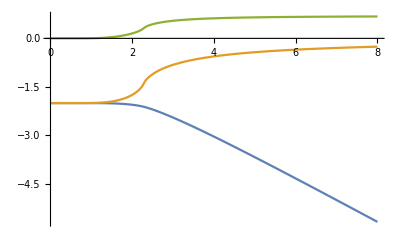

```mathematica
Plot[{f[t,n],u[t,n],s[t,n]},{t,10^-3,8}]
```

{2.283,2.2756039}

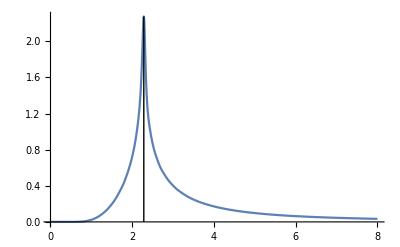

```mathematica
tab=Table[{t,Evaluate@cv[t,n]},{t,2,3,0.0005}];{Subscript[t, c],max}=Block[{maxx=Max@(Transpose@tab)⟦2⟧},{tab⟦Position[tab,maxx]⟦1,1⟧,1⟧,maxx}]
Plot[cv[t,n],{t,10^-3,8},PlotRange->All,Epilog->{Line@{{Subscript[t, c],0},{Subscript[t, c],max}}}]
```

### Errors

```mathematica
ef[t_,n_]:=f[t,n]-fx[t,n];
eu[t_,n_]:=u[t,n]-ux[t,n];
es[t_,n_]:=s[t,n]-sx[t,n];
Plot[{ef[t,n],eu[t,n],es[t,n]},{t,0.01,8},PlotRange->All,PlotLegends->{"f","u","s"}]
```

$Aborted

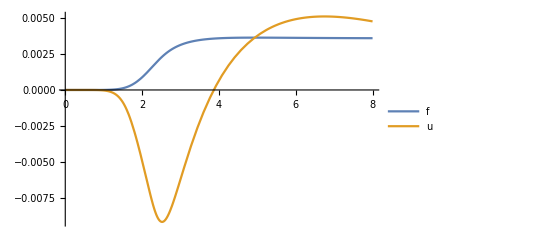

```mathematica
Plot[{ef[t,n]/fx[t,n],eu[t,n]/ux[t,n]},{t,0.01,8},PlotRange->All,PlotLegends->{"f","u","s"}]
```

```mathematica
collectTc[list_]:=Module[{stream,info,edge,d,n,ch,i,ϵ,g,glog,tab,t,max,u,Z,cv},
stream=OpenRead[inputFile[#,1]];
info=StringSplit[ReadList[stream,String],": "];
Close[stream];

{i,ϵ,g,glog}=readRun[#,1];

edge=getProp[info,"edge_length"];
d=getProp[info,"dimensionality"];
n=edge^d;
ch=Length@g;
Z[t_]:=∑_(j=1)^ch g⟦j⟧ⅇ^(-ϵ⟦j⟧/t);
u[t_,n_]:=1/(n Z[t])∑_(j=1)^ch ϵ⟦j⟧g⟦j⟧ⅇ^(-ϵ⟦j⟧/t);

cv[t_,n_]:=D[u[tt,n], tt]/.tt->t;
tab=Table[{t,Evaluate@cv[t,n]},{t,2,2.5,0.001}];
Block[{maxx=Max@(Transpose@tab)⟦2⟧},{edge,tab⟦Position[tab,maxx]⟦1,1⟧,1⟧, max}]

]&/@list
```

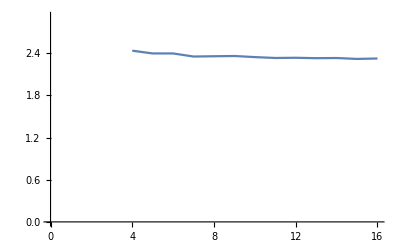

```mathematica
{l,tc,cvm}=collectTc[{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,24,32,64}];
ListPlot[{l,tc},Joined->True,PlotRange->{{0,16},1.5{0,Max[(Transpose@tc)⟦2⟧]}}]
ListPlot[{l,cvm},Joined->True,PlotRange->{{0,16},1.5{0,Max[(Transpose@tc)⟦2⟧]}}]
```